```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab10\lab10\lab10

```mathematica
R = Import["R.txt","List"]
```

{0.199999,-6.47061×10^-7,-6.26706×10^-7,-6.11471×10^-7,0.066666,-6.33679×10^-7,-6.24774×10^-7,-6.16997×10^-7,0.0399994,-6.30159×10^-7,-6.24418×10^-7,-6.19165×10^-7,0.0285708,-6.28535×10^-7,-6.24293×10^-7,-6.20323×10^-7,0.0222216,-6.27601×10^-7,-6.24235×10^-7,-6.21043×10^-7,0.0181812,-6.26993×10^-7,-6.24204×10^-7,-6.21534×10^-7,0.015384,-6.26567×10^-7,-6.24185×10^-7,-6.21891×10^-7,0.0133327,-6.26251×10^-7,-6.24172×10^-7,-6.22161×10^-7,0.0117641,-6.26008×10^-7,-6.24164×10^-7,-6.22373×10^-7,0.0105257,-6.25815×10^-7,-6.24158×10^-7,-6.22544×10^-7,0.00952318,-6.25658×10^-7,-6.24154×10^-7,-6.22685×10^-7,0.00869503,-6.25528×10^-7,-6.2415×10^-7,-6.22803×10^-7,0.00799937,-6.25418×10^-7,-6.24148×10^-7,-6.22903×10^-7,0.00740678,-6.25324×10^-7,-6.24145×10^-7,-6.22989×10^-7,0.00689593,-6.25243×10^-7,-6.24144×10^-7}

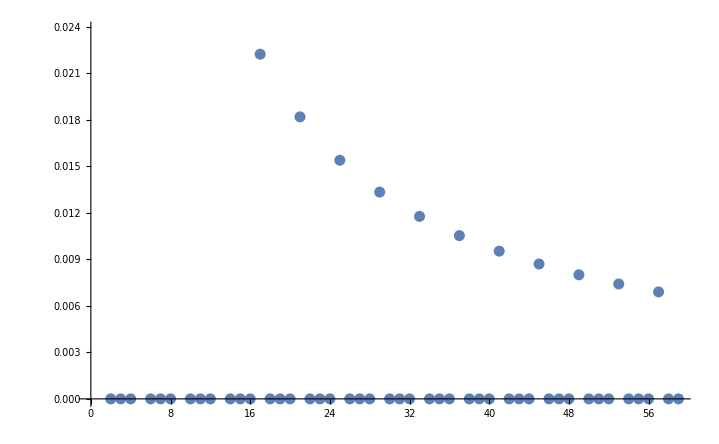

```mathematica
ListPlot[R]
```

```mathematica
k = Import["test_k.txt","Table"]
```

{{0.900969,0.433884},{0.222521,0.974928},{-0.623489,0.781832},{-1.,6.5359×10^-7},{-0.62349,-0.781831},{0.22252,-0.974928},{0.900968,-0.433885}}

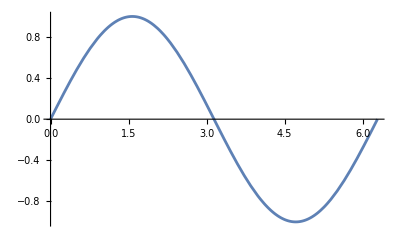

```mathematica
Show[Plot[Sin[x],{x,0,2Pi}],ListPlot[Table[{k[[i]],Sin[ArcTan[(k[[i]][[2]])/(k[[i]][[1]])]]},{i,Length@k}],PlotStyle->Red,PlotRange->All]]
```

```mathematica
k
```

{{0.900969,0.433884},{0.222521,0.974928},{-0.623489,0.781832},{-1.,6.5359×10^-7},{-0.62349,-0.781831},{0.22252,-0.974928},{0.900968,-0.433885}}

```mathematica
Table[{k[[i]],Sin[ArcTan[(k[[i]][[2]])/(k[[i]][[1]])]]},{i,Length@k}]
```

{{{0.900969,0.433884},0.433884},{{0.222521,0.974928},0.974928},{{-0.623489,0.781832},-0.781832},{{-1.,6.5359×10^-7},-6.5359×10^-7},{{-0.62349,-0.781831},0.781831},{{0.22252,-0.974928},-0.974928},{{0.900968,-0.433885},-0.433885}}

```mathematica
Sin[ArcTan[(k[[i]][[2]])/(k[[i]][[1]])]]/.i->1
```

Part::pkspec1: The expression i cannot be used as a part specification.

{{0.742936,0.917371},{0.976125,0.716026},{-0.848574,0.787802},{-0.707107,1.},{-0.848574,-0.787802},{0.976125,-0.716026},{0.742936,-0.917371}}